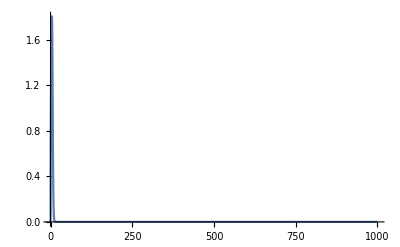

```mathematica
Plot[x^(3/2-1)/(( 500)^-1 Exp[x]+1),{x,0,1000},PlotRange->All]
```

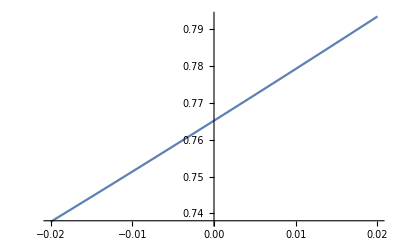

```mathematica
z0 = 0; dz=0.02;
Plot[-PolyLog[3/2,-10^z],{z,z0-dz,z0+dz}]
```

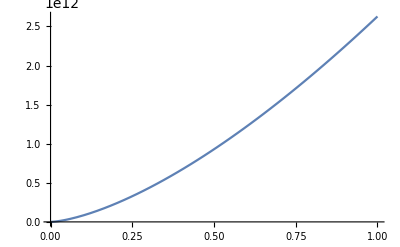

```mathematica
Plot[-PolyLog[3/2,-10^z],{z,0,100000000}]
```

```mathematica
m=3/2;z=Exp[5000];1/Factorial[m-1] NIntegrate[x^(m-1)/((z)^-1 Exp[x]+1),{x,0,Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4974.36}. NIntegrate obtained 235555. and 2652.99 for the integral and error estimates.

265795.

```mathematica
1/Factorial[m-1] Integrate[x^(m-1)/(z^-1 Exp[x]+1),{x,0,Infinity}]
```

ConditionalExpression[-(Gamma[m] PolyLog[m,-z])/((-1+m)!),Re[m]>0]

```mathematica
NumberForm[N[Re[-PolyLog[3/2,-Exp[500]]]],20]
```

8410.48324407698

```mathematica
data = Table[{z,Re[-PolyLog[3/2,-10^z]]},{z,0,100,0.01}];
```

```mathematica
polyfit = Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20,x^21,x^22,x^23,x^24,x^25,x^26,x^27,x^28,x^29,x^30},x]/.{x->z}
```

0.785151+1.18092 z+1.50656 z^2-0.205859 z^3+0.0274319 z^4-0.00271924 z^5+0.00019655 z^6-0.0000103933 z^7+4.02195×10^-7 z^8-1.12584×10^-8 z^9+2.19915×10^-10 z^10-2.71416×10^-12 z^11+1.39445×10^-14 z^12+1.20361×10^-16 z^13-1.95319×10^-18 z^14-4.18668×10^-21 z^15+1.88535×10^-22 z^16+3.57481×10^-25 z^17-1.7671×10^-26 z^18-6.74828×10^-29 z^19+1.56387×10^-30 z^20+1.13147×10^-32 z^21-1.22508×10^-34 z^22-1.53779×10^-36 z^23+8.74405×10^-39 z^24+1.81314×10^-40 z^25-8.88855×10^-43 z^26-1.922×10^-44 z^27+2.34292×10^-46 z^28-1.01683×10^-48 z^29+1.63058×10^-51 z^30

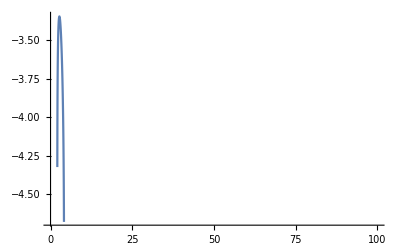

```mathematica
Plot[Log10[(-PolyLog[3/2,-10^z]-polyfit)/(-PolyLog[3/2,-10^z])],{z,0,100}]
```

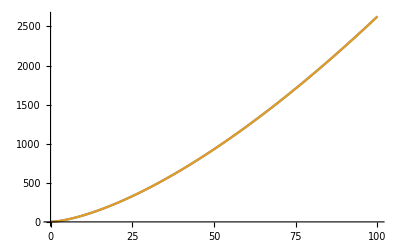

```mathematica
Plot[{-PolyLog[3/2,-10^z],polyfit},{z,0,100}]
```

```mathematica
dataNeg = Table[{z,Re[-PolyLog[3/2,-10^z]]},{z,-5,0,0.01}];
```

```mathematica
polyfitNeg = Fit[dataNeg,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19,x^20,x^21,x^22,x^23,x^24,x^25,x^26,x^27,x^28,x^29,x^30},x]/.{x->z}
```

0.765147+1.39283 z+1.00769 z^2+0.241867 z^3-0.10129 z^4-0.0486696 z^5+0.0291692 z^6+0.00593046 z^7-0.0362557 z^8-0.0397364 z^9-0.0208443 z^10-0.00604082 z^11-0.00071855 z^12+0.000100618 z^13+0.0000371446 z^14-1.33529×10^-6 z^15-1.40852×10^-6 z^16+5.05116×10^-8 z^17+5.19597×10^-8 z^18-3.98738×10^-9 z^19-1.80003×10^-9 z^20+2.64116×10^-10 z^21+5.48657×10^-11 z^22-1.40824×10^-11 z^23-1.51765×10^-12 z^24+6.53319×10^-13 z^25+6.10896×10^-14 z^26-2.74085×10^-14 z^27-6.55479×10^-15 z^28-5.62172×10^-16 z^29-1.78488×10^-17 z^30

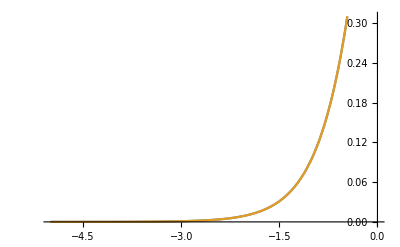

```mathematica
Plot[{-PolyLog[3/2,-10^z],polyfitNeg},{z,-5,0}]
```

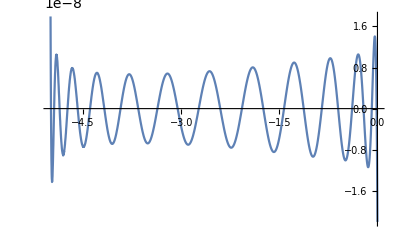

```mathematica
Plot[-PolyLog[3/2,-10^z]-polyfitNeg,{z,-5,0}]
```

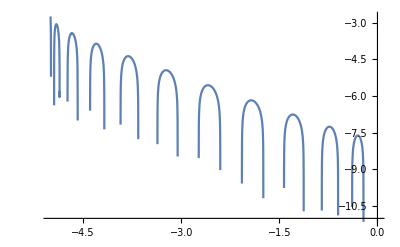

```mathematica
Plot[Log10[(-PolyLog[3/2,-10^z]-polyfitNeg)/(-PolyLog[3/2,-10^z])],{z,-5,0}]
```

```mathematica
dataFile = Table[{z,Re[-PolyLog[3/2,-Exp[z]]]},{z,-10000,10000,0.02}];
```

```mathematica
Export["FermiDensityPolyLog.csv",dataFile]
```

FermiDensityPolyLog.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["FermiDensityPolyLog.csv"]]]
```

```mathematica
N[Re[-PolyLog[3/2,-Exp[50 10^3]]]]
```

8.41044×10^6